```mathematica
ClearAll[Veff,firstOrderPot,firstOrderCritPts,ϕs,Veff2,secondOrderPot,ϕ2s,secondOrderCritPts]
```

```mathematica
Veff[ϕ_,t_]:=((-0.1^2/2+a t^2)ϕ^2-b t ϕ^3+0.1^2/4 ϕ^4)/.{a->0.2,b->0.03}
```

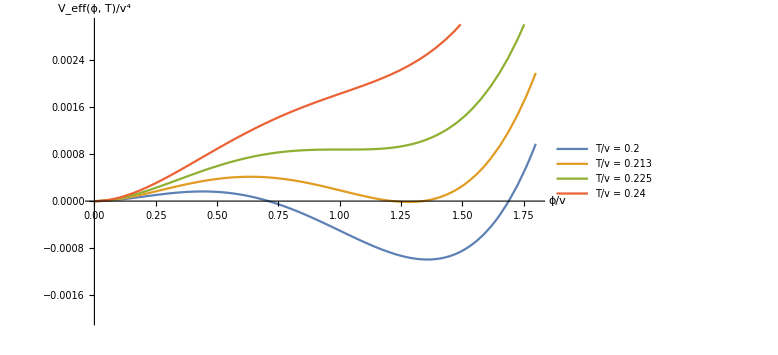

```mathematica
firstOrderPot=Plot[Table[Veff[ϕ,t],{t,{0.2,0.213,0.225,0.24}}]//Evaluate,{ϕ,0,1.8},ImageSize->Large,AxesLabel->{"ϕ/v","V_eff(ϕ, T)/v^4"},LabelStyle->Larger,PlotLegends->{Table[StringJoin["T/v = ", ToString[t]],{t,{0.2,0.213,0.225,0.24}}]},PlotRange->{{0,1.8},{-0.002,0.003}}]
```

```mathematica
Export[FileNameJoin[{ParentDirectory[DirectoryName[NotebookFileName[]]], "images", "ch1", "first_order_free_energy.eps"}],firstOrderPot]
```

C:\Users\Michael\Dropbox\PhD-thesis\images\ch1\first_order_free_energy.eps

```mathematica
ϕs=Solve[D[Veff[ϕ,t],ϕ]==0,ϕ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϕ→0.},{ϕ→0.5 (9. t-1. √(4.-79. t^2))},{ϕ→0.5 (9. t+√(4.-79. t^2))}}

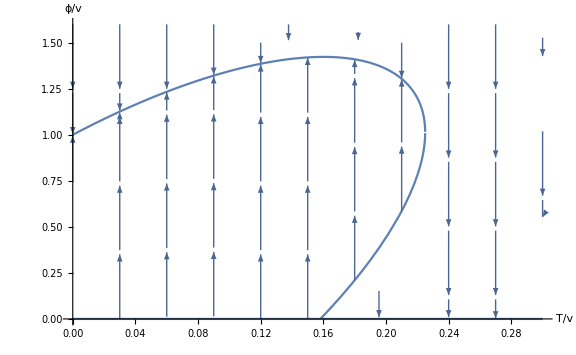

```mathematica
firstOrderCritPts=Show[
Plot[ϕ/.ϕs,{t,0,0.3},PlotRange->{{0,0.3},{0,1.6}},ImageSize->Large,AxesLabel->{"T/v","ϕ/v"},LabelStyle->Larger],
StreamPlot[{0,-D[Veff[ϕ2,t],ϕ2]/.ϕ2->ϕ//Evaluate},{t,0,0.3},{ϕ,0,1.6},PlotRange->{{0,0.3},{0,1.6}},StreamScale->1,StreamStyle->Arrowheads[0.05],StreamPoints->(Flatten[#,1]&@Table[{{x,0},{x,0.75},{x,1.5}},{x,0,0.3,0.01}])]
]
```

```mathematica
Export[FileNameJoin[{ParentDirectory[DirectoryName[NotebookFileName[]]], "images", "ch1", "first_order_free_energy_critical_pts.eps"}],firstOrderCritPts]
```

C:\Users\Michael\Dropbox\PhD-thesis\images\ch1\first_order_free_energy_critical_pts.eps

```mathematica
Veff2[ϕ_,t_]:=0.0029((ϕ^2+((t^2-0.158^2)/0.158^2))^2-((t^2-0.158^2)/0.158^2)^2);
```

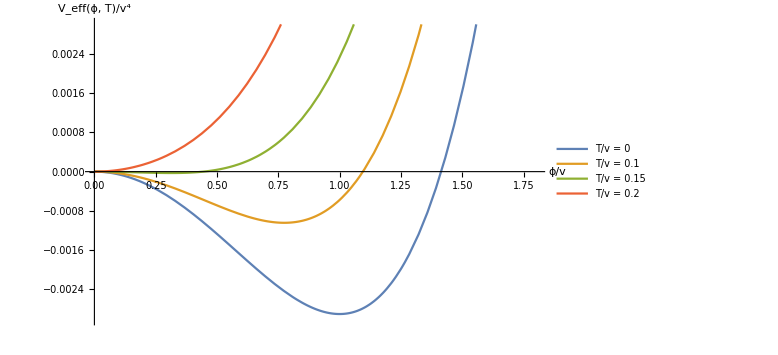

```mathematica
secondOrderPot=Plot[Table[Veff2[ϕ,t],{t,{0,0.1,0.15,0.2}}]//Evaluate,{ϕ,0,1.8},ImageSize->Large,AxesLabel->{"ϕ/v","V_eff(ϕ, T)/v^4"},LabelStyle->Larger,PlotLegends->{Table[StringJoin["T/v = ", ToString[t]],{t,{0,0.1,0.15,0.2}}]},PlotRange->{{0,1.8},{-0.003,0.003}}]
```

```mathematica
Export[FileNameJoin[{ParentDirectory[DirectoryName[NotebookFileName[]]], "images", "ch1", "second_order_free_energy.eps"}],secondOrderPot]
```

C:\Users\Michael\Dropbox\PhD-thesis\images\ch1\second_order_free_energy.eps

```mathematica
ϕ2s=Solve[D[Veff2[ϕ,t],ϕ]==0,ϕ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϕ→0},{ϕ→-0.0126582 √(6241.-250000. t^2)},{ϕ→0.0126582 √(6241.-250000. t^2)}}

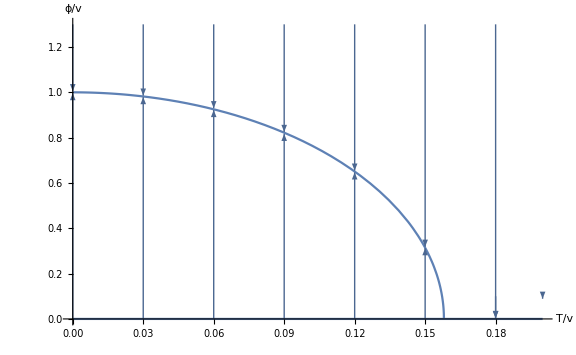

```mathematica
secondOrderCritPts=Show[
Plot[ϕ/.ϕ2s,{t,0,0.2},PlotRange->{{0,0.2},{0,1.3}},ImageSize->Large,AxesLabel->{"T/v","ϕ/v"},LabelStyle->Larger],
StreamPlot[{0,-D[Veff2[ϕ2,t],ϕ2]/.ϕ2->ϕ//Evaluate},{t,0,0.2},{ϕ,0,1.3},PlotRange->{{0,0.2},{0,1.3}},StreamScale->Full,StreamStyle->Arrowheads[0.05],StreamPoints->(Flatten[#,1]&@Table[{{x,0.1},{x,1.2}},{x,0,0.2,0.01}])]
]
```

```mathematica
Export[FileNameJoin[{ParentDirectory[DirectoryName[NotebookFileName[]]], "images", "ch1", "second_order_free_energy_critical_pts.eps"}],secondOrderCritPts]
```

C:\Users\Michael\Dropbox\PhD-thesis\images\ch1\second_order_free_energy_critical_pts.eps